### LDR to HDR conversion

We’re attempting to find the best fitting method and curves when provided a “camera response curve” computed by singular value decomposition of a matrix of LDR pixel values picked from multiple LDR images.
The resulting response curve is more or less defined as log2(f(Zi)) for various Zi values in [0,255] (or [0,4905] if the source images are 12-bits RAW) where f(x) is the response curve we’re attempting to fit.

```mathematica
ClearAll["Global`*"]
```

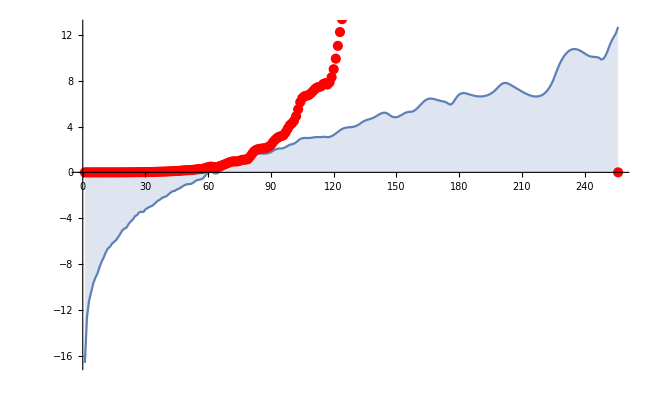

```mathematica
(* Import binary data as a 256 entry float array *)
tentFilter[x_]=1-Abs[x-128]/128;
SetDirectory[NotebookDirectory[]]; 
rawCurve = BinaryReadList["../../responseCurve9.float","Real32"];
rawCurveLinear=Table[tentFilter[i]* 2^rawCurve[[i]],{i,1,256}];
Show[ListLinePlot[rawCurve,Filling->Axis],ListPlot[rawCurveLinear,PlotStyle->Red]]
```

{a→16.9989,b→691.248,c→-1.01688,d→0.00877215}

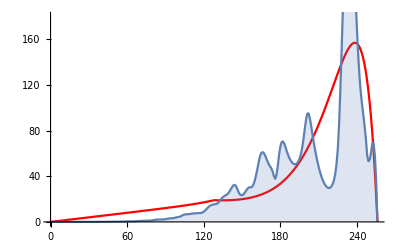

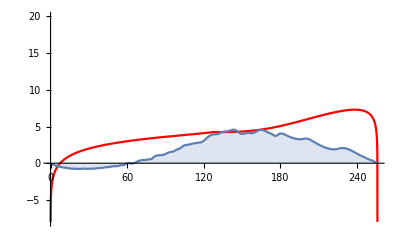

```mathematica
(* Try and fit the curve in log2 space *)
fittingMethod="PrincipalAxis";
fittingMethod="LevenbergMarquardt";
fittingMethod="Automatic";
data = rawCurveLinear;
model =tentFilter[x]*Exp[ a+ b*x^c]; (* Cool! with a=0, b=2, c=0, d=0 *)
model =tentFilter[x]*Exp[ a+ b*x^c]; (* Cool! with a=0, b=2, c=0, d=0 *)
model =tentFilter[x]*( a+b^(c+d*x));
modelFit=FindFit[data,model,{{a,0},{b,1},{c,0.1},{d,0}},{x},Method->fittingMethod]

model=Function[{x},Evaluate[model/.modelFit]];
(*Plot[model[x],{x,0,256},PlotRange->{-20,16}]*)
Show[ 
 Plot[model[x],{x,0,256},PlotRange->{0,180},PlotStyle->Red],
ListLinePlot[data,PlotRange->{0,1000},Filling->Axis]
]
Show[ 
 Plot[Log2[model[x]],{x,0,256},PlotRange->{-8,20},PlotStyle->Red],
ListLinePlot[Table[tentFilter[x]*rawCurve[[x]],{x,1,256}],PlotRange->Full,Filling->Axis]
]
```

FindFit::lmnl: The model (a + b\ x + c\ x^2 + d\ x^3)\ (1 - 1/128\ Abs[-128 + x]) is linear in the parameters {a, b, c, d}, but a nonlinear method or non-Euclidean norm was specified, so nonlinear methods will be used.

{a→-6.55077,b→0.1263,c→-0.000435788,d→7.52068×10^-7}

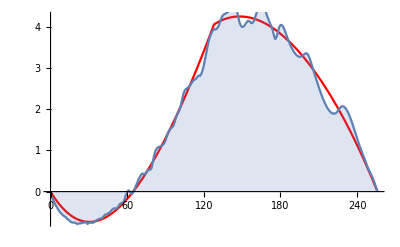

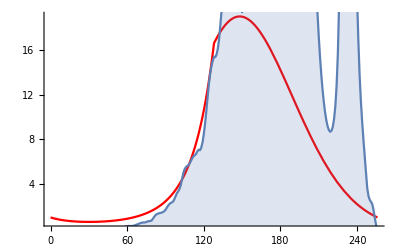

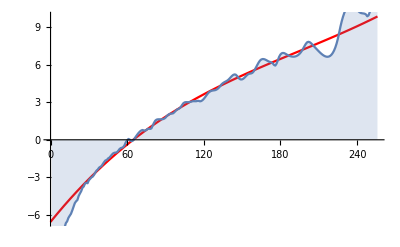

```mathematica
data = Table[tentFilter[x]*rawCurve[[x]],{x,1,256}];
model =tentFilter[x]*(a+b*x+c*x^2);
model =tentFilter[x]*(a+b*x+c*x^2+d*x^3);

fittingMethod="Automatic";
fittingMethod="LevenbergMarquardt";
fittingMethod="PrincipalAxis";
fittingMethod="NMinimize";
fittingMethod="Newton";
fittingMethod="InteriorPoint";
fittingMethod="ConjugateGradient";
fittingMethod="Gradient";
fittingMethod="QuasiNewton";

modelFit=FindFit[data,model,{{a,0},{b,1},{c,0.1},{d,0}},{x},Method->fittingMethod]

model=Function[{x},Evaluate[model/.modelFit]];
Show[ 
 Plot[model[x],{x,0,256},PlotRange->Full,PlotStyle->Red],
ListLinePlot[data,PlotRange->Full,Filling->Axis]
]
Show[ 
 Plot[Power[2,model[x]],{x,0,256},PlotRange->Full,PlotStyle->Red],
ListLinePlot[Table[tentFilter[x]*rawCurveLinear[[x]],{x,1,256}],PlotRange->Full,Filling->Axis]
]
model=Function[{x},Evaluate[a+b*x+c*x^2+d*x^3/.modelFit]];
Show[ 
 Plot[model[x],{x,0,256},PlotRange->Full,PlotStyle->Red],
ListLinePlot[rawCurve,PlotRange->Full,Filling->Axis]
]
```